time: 15. μs

using a time step of 0.01 μs

7.5×10^9

5.07634×10^6

3.

0.00011

1.07368

1.01717

-2.40641×10^7

power broadening :0.000255512

resonance defect :0.00011

verhältnis: 1:0.430508

2.40641×10^7

chirp step: 1.5×10^7

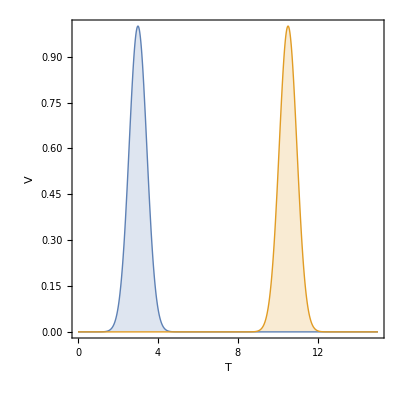

-0.536841 | 0. | -1.20321×10^7 | 1.20321×10^7 | 0. | 0.
0. | 0.536841 | 1.20321×10^7 | 1.20321×10^7 | 0. | 0.
-1.20321×10^7 | 1.20321×10^7 | 0.+0. ⅈ | 0. | 2.37167×10^-56 | -2.37167×10^-56
1.20321×10^7 | 1.20321×10^7 | 0. | 2.07202×10^7+0. ⅈ | 2.37167×10^-56 | 2.37167×10^-56
0. | 0. | 2.37167×10^-56 | 2.37167×10^-56 | -0.508586 | 0.
0. | 0. | -2.37167×10^-56 | 2.37167×10^-56 | 0. | 0.508586

{0.155462,Null}

last state vector: {-0.30323+0.372246 ⅈ,-0.347234+0.372248 ⅈ,-0.657284-0.258861 ⅈ,-0.105141+0.0160502 ⅈ,1.26037×10^-11+7.10086×10^-12 ⅈ,-7.53244×10^-12-6.30788×10^-12 ⅈ}

last population: {0.230516,0.25914,0.499032,0.0113122,2.09274×10^-22,9.65271×10^-23}

final norm: 1.

-0.536841 | 0. | -2.37167×10^-56 | 2.37167×10^-56 | 0. | 0.
0. | 0.536841 | 2.37167×10^-56 | 2.37167×10^-56 | 0. | 0.
-2.37167×10^-56 | 2.37167×10^-56 | 0.+0. ⅈ | 0. | 1.20321×10^7 | -1.20321×10^7
2.37167×10^-56 | 2.37167×10^-56 | 0. | 2.07202×10^7+0. ⅈ | 1.20321×10^7 | 1.20321×10^7
0. | 0. | 1.20321×10^7 | 1.20321×10^7 | -0.508586 | 0.
0. | 0. | -1.20321×10^7 | 1.20321×10^7 | 0. | 0.508586

```mathematica
ClearAll["`*"];
(* this calculates a two Raman Adiabatic Passages using two frequency-chirped pulses *)
(* Example: Cl2O2, also calculates the evolution of the wavepacket's parity *)
NT = 1501;
NT2=IntegerPart[NT/2]+1;
dt =0.01 ;
sq2=Sqrt[2.];
ℏ=10^6; (* account for the Hamiltonian given in 1/μs *)
Print["time: ", (NT-1)*dt, " μs"]
Print["using a time step of ", dt, " μs"]

(* laser field parameter for cl2o2, D and W cm^-2 *)
μP =3.2*10^-6;
μS =-1.23*10^-4;
IP0=7.5*10^9
IS0=IP0*(μP/μS)^2 
(*line shape*)
τP=3.
τS=τP+NT2*dt;
τ=.625;

(* Molecular Parameter for Cl2O2*)
Δ1=2π* 2. 10^3; (*ca. 7. 10^-8 cm^-1 *)
Δ3=2π* 0.5 10^3; (* ca. 1.7 10^-8 cm^-1 *)
c=2.99792458*10^10;
x2=1.1*10^-4
Δ2 =  2*π*c*x2; (* ca. 3. 10^-3 cm^-1 *)
ΔE12= 2*π*c*5.7*10^-12 (* ca. 10^-12 cm^-1 *)
ΔE23= 2*π*c*5.4*10^-12
Γ=0*10^6.;


IIP[t_]:=IP0*Exp[-2*(t-τP)^2/τ^2](*;*UnitStep[t-2.5]*UnitStep[-(t-2.5-2*τ)];*)
IIS[t_]:=IS0*Exp[-2*(t-τS)^2/τ^2];
VP[t_]:=-μP*Sqrt[IIP[t]]*86833957;
VS[t_]:=-μS*Sqrt[IIS[t]]*86833957;
(* power broadening *)
VP[τP]
Print["power broadening :", 2*0.461*μP*Sqrt[IP0/10^6]]
Print["resonance defect :", x2]
Print["verhältnis: 1:", x2/(2*0.461*μP*Sqrt[IP0/10^6])]
VS[τS]

(* chrip parameters *)

δchirp = 15.*10^6;
Print["chirp step: ", δchirp]
d[t_] := If[t<dt*NT2,(τP-t)*2*δchirp,(τS-t)*2*δchirp];

Plot[{VP[t]/VP[τP],VS[t]/VS[τS]},{t,0,NT*dt},PlotRange->{All,All},Filling->Axis,
PlotStyle->{Thick,Thick},Frame->True,Axes->{False,False},ImageSize->400,AspectRatio->1,
FrameLabel->{"T","V"},LabelStyle->Directive[FontFamily->"Times",FontSize->14]]

ΗpvCl[t_] := 0.5*{{-ΔE12,0,VP[t],-VP[t],0,0},
                 {0,ΔE12,-VP[t],-VP[t],0,0},
                 {VP[t],-VP[t],0-ⅈ*Γ+d[t],0,VS[t],-VS[t]},
                 {-VP[t],-VP[t],0,2*Δ2-ⅈ*Γ+d[t],VS[t],VS[t]},
                 {0,0,VS[t],VS[t],-ΔE23,0},
                 {0,0,-VS[t],VS[t],0,ΔE23}};
ΗpvCl[τP]//TableForm
(* initial sate vecotrs *)
p=Table[0,{i,NT},{j,6}];
p2=Table[0,{i,NT+1},{j,6}];

(* Integrate the Hamiltonian Matrix for a given time interval *)

DistributeDefinitions[ΗpvCl];
(* initialize dynamics *)
pp= {1/Sqrt[2],+1/Sqrt[2],0,0,0,0};
pm= {1/Sqrt[2],-1/Sqrt[2],0,0,0,0};
pR = {0,1,0,0,0,0};
pL = {1,0,0,0,0,0};
p[[1]] =pL; 
p2[[1]]=pp;
wfc=Table[{0,0,0,0},{t,1,2*NT}];
Do[
	wfc[[i,1]]=1;	
	wfc[[i,2]]=Switch[i,1,1,2,2,3,11,4,12,5,23,6,24];
    wfc[[i,3]]=Re[p[[1,i]]];
	wfc[[i,4]]=Im[p[[1,i]]]
 ,{i,1,6}];
Monitor[
Do[
p[[t]]=MatrixExp[-ⅈ*ΗpvCl[(t-1)*dt+dt/2.]*dt/ℏ].p[[t-1]];
If[Mod[t+5,6]==0,
Do[
	Switch[i,1,j=1,2,j=2,3,j=5,4,j=6,5,j=3,6,j=4];
    wfc[[(IntegerPart[(t+5)/6]-1)*6+i,1]]=IntegerPart[(t+5)/6];	
	wfc[[(IntegerPart[(t+5)/6]-1)*6+i,2]]=Switch[j,1,1,2,2,3,23,4,24,5,11,6,12];
    wfc[[(IntegerPart[(t+5)/6]-1)*6+i,3]]=Re[p[[t,j]]];
	wfc[[(IntegerPart[(t+5)/6]-1)*6+i,4]]=Im[p[[t,j]]];
 ,{i,1,6}]],
{t,2,NT2} ],ProgressIndicator[t/NT2]];//Timing
(* check norm of the wavefunction *)
Table[{(t-1)*dt,Sum[Abs[p[[t,i]]]^2,{i,1,4}]},{t,1,NT2}];
(*ListLinePlot[Table[{(t-1)*dt,Sum[Abs[p[[t,i]]]^2,{i,1,4}]},{t,1,NT}],PlotRange->{All,{1-10^-5,1+10^-5}}]*)
Print["last state vector: ", p[[NT2]]]
Print["last population: ", Abs[p[[NT2]]]^2]
Print["final norm: ",Conjugate[p[[NT2]]].p[[NT2]]//Chop]

(* -----------------now the down pulse------------------- *)

ΗpvCl[t_] := 0.5*{{-ΔE12,0,VP[t],-VP[t],0,0},
                 {0,ΔE12,-VP[t],-VP[t],0,0},
                 {VP[t],-VP[t],0-ⅈ*Γ+d[t],0,VS[t],-VS[t]},
                 {-VP[t],-VP[t],0,2*Δ2-ⅈ*Γ+d[t],VS[t],VS[t]},
                 {0,0,VS[t],VS[t],-ΔE23,0},
                 {0,0,-VS[t],VS[t],0,ΔE23}};
ΗpvCl[τS]//TableForm
wfc2=Table[{0,0,0,0},{t,1,NT+1}];
```

{0.158727,Null}

wavefunction_coefficients.out

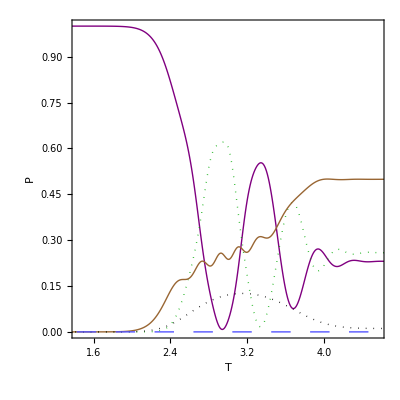

last state vector: {-0.30323+0.372246 ⅈ,-0.347234+0.372248 ⅈ,-0.657284-0.258861 ⅈ,-0.105141+0.0160502 ⅈ,1.26037×10^-11+7.10086×10^-12 ⅈ,-7.53244×10^-12-6.30788×10^-12 ⅈ}

last population: {0.230516,0.25914,0.499032,0.0113122,2.09274×10^-22,9.65271×10^-23}

final norm: 1.

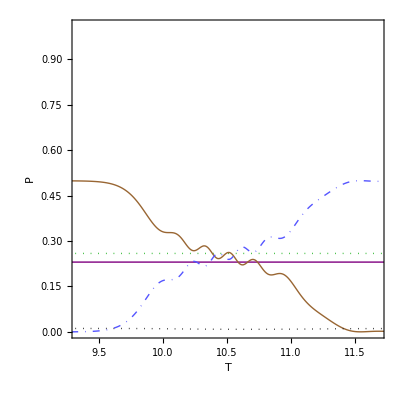

last state vector: {-0.303231+0.372245 ⅈ,-0.347233+0.372249 ⅈ,0.0310045-0.0022618 ⅈ,0.03712-0.0983787 ⅈ,-0.487591-0.101456 ⅈ,0.4847+0.123893 ⅈ}

last population: {0.230516,0.25914,0.000966394,0.0110563,0.248038,0.250284}

final norm: 1.

{-0.487591-0.101456 ⅈ,0.4847+0.123893 ⅈ}

{0.248038,0.250284}

populations in λ, ρ: 0.498321

b+ -0.00204384-0.0158654 ⅈ

b- -0.687513+0.159346 ⅈ

population of superposition χ+: 0.000255889  χ-: 0.498066

1.

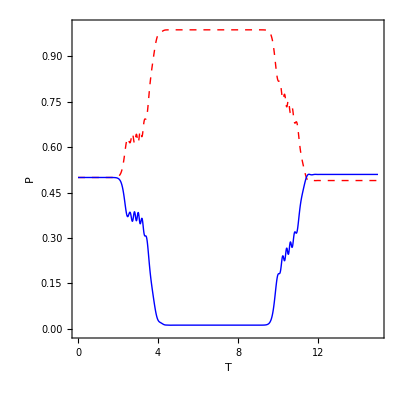

```mathematica
Monitor[
Do[
p[[t]]=Quiet[MatrixExp[-ⅈ*ΗpvCl[(t-1)*dt+dt/2.]*dt/ℏ].p[[t-1]]];
If[Mod[t+5,6]==0,
Do[
	Switch[i,1,j=1,2,j=2,3,j=5,4,j=6,5,j=3,6,j=4];
    wfc[[(IntegerPart[(t+5)/6]-1)*6+i,1]]=IntegerPart[(t+5)/6];	
	wfc[[(IntegerPart[(t+5)/6]-1)*6+i,2]]=Switch[j,1,1,2,2,3,23,4,24,5,11,6,12];
    wfc[[(IntegerPart[(t+5)/6]-1)*6+i,3]]=Re[p[[t,j]]];
	wfc[[(IntegerPart[(t+5)/6]-1)*6+i,4]]=Im[p[[t,j]]];
 ,{i,1,6}]],
{t,NT2+1,NT} ],ProgressIndicator[t/NT2]];//Timing(* check norm of the wavefunction *)
Table[{(t-1)*dt,Sum[Abs[p[[t,i]]]^2,{i,1,4}]},{t,NT2+1,NT}];
Export["wavefunction_coefficients.out",wfc,"Table"]
(* ------------ *)
Show[{(*Plot[VP[t]/VP[τP],{t,1,dt*NT},Filling->Axis,PlotRange->{{τP-3*τ^2,τP+3*τ^2},{0,1.}},PlotStyle->Black,FillingStyle->Directive[Opacity[0.05],Purple]],
*)ListLinePlot[ {
Table[{(t-1)*dt,Abs[p[[t,1]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,2]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,3]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,4]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,5]]]^2+Abs[p[[t,6]]]^2},{t,1,NT}]}
,PlotRange->{{Max[0,τP-4*τ^2],τP+4*τ^2},{0,1.}},PlotStyle->{Directive[Purple,Thick],Directive[Thick,Darker[Green],Dotted],Directive[Brown,Thick],
Directive[Black,Dotted,Thick],Directive[Lighter[Blue],Thick,Dashing[Large]],Directive[Gray,Dotted]}]
},Frame->True,FrameLabel->{"T","P"},Axes->{False,False},ImageSize->400,AspectRatio->1,
LabelStyle->Directive[FontFamily->"Times",FontSize->26]]

Print["last state vector: ", p[[NT2]]]
Print["last population: ", Abs[p[[NT2]]]^2]
Print["final norm: ",Conjugate[p[[NT2]]].p[[NT2]]//Chop]

(*ListLinePlot[Table[{(t-1)*dt,Sum[Abs[p[[t,i]]]^2,{i,1,4}]},{t,1,NT}],PlotRange->{All,{1-10^-5,1+10^-5}}]*)
(* ------------ *)
Show[{(*Plot[VS[t]/VS[τS],{t,1,dt*NT},Filling->Axis,PlotRange->{{τS-3*τ^2,τS+3*τ^2},{0,1.}},PlotStyle->Black,FillingStyle->Directive[Opacity[0.05],Purple]],*)
ListLinePlot[ {
Table[{(t-1)*dt,Abs[p[[t,1]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,2]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,3]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,4]]]^2},{t,1,NT}],
Table[{(t-1)*dt,Abs[p[[t,5]]]^2+Abs[p[[t,6]]]^2},{t,1,NT}]}
,PlotRange->{{τS-3*τ^2,Min[τS+3*τ^2,NT*dt]},{0,1.01}},PlotStyle->{Directive[Purple,Thick],Directive[Thick,Darker[Green],Dotted],Directive[Brown,Thick],
Directive[Black,Dotted,Thick],Directive[Lighter[Blue],Thick,DotDashed],Directive[Gray,Dotted]}]
},Frame->True,FrameLabel->{"T","P"},Axes->{False,False},ImageSize->400,AspectRatio->1,
LabelStyle->Directive[FontFamily->"Times",FontSize->26]]

Print["last state vector: ", p[[NT]]]
Print["last population: ", Abs[p[[NT]]]^2]
Print["final norm: ",Conjugate[p[[NT]]].p[[NT]]//Chop]


avψ=Table[Abs[p[[t,3]]]^2-Abs[p[[t,4]]]^2 ,{t,1,NT}];
avψ2=Table[ 2*Re[ Conjugate[p[[t,1]]] * p[[t,2]] ],{t,1,NT}];
(*ListLinePlot[avψ,PlotRange->{All,{0,1}}]
ListLinePlot[avψ+avψ2,PlotRange->{All,{0,1}}]*)
(* -------- check for parity ----- *)
(* project out λ-ρ *)
ψ={p[[NT,5]],p[[NT,6]]}
Abs[ψ]^2
Print["populations in λ, ρ: ",np=Conjugate[ψ].ψ //Chop]
ϕp={1/sq2,1/sq2};
ϕm={1/sq2,-1/sq2};
Print["b+ ",pplus=Conjugate[ψ].ϕp]
Print["b- ",pmin=Conjugate[ψ].ϕm]
Print["population of superposition χ+: ",Abs[pplus]^2,"  χ-: ",Abs[pmin]^2]
1/np*(Conjugate[ψ].ϕp//Abs)^2+1/np*(Conjugate[ψ].ϕm//Abs)^2
TrafoParity=1/sq2*{{1,1,0,0,0,0},{1,-1,0,0,0,0},{0,0,sq2,0,0,0},{0,0,0,sq2,0,0},{0,0,0,0,1,1},{0,0,0,0,1,-1}};
plotpar=Table[Abs[ TrafoParity.p[[t]]]^2,{t,1,NT}];

ListLinePlot[ {
Table[{(t-1)*dt,plotpar[[t,1]]+plotpar[[t,3]]+plotpar[[t,5]]},{t,1,NT}]
,Table[{(t-1)*dt,plotpar[[t,2]]+plotpar[[t,4]]+plotpar[[t,6]]},{t,1,NT}]}
,PlotRange->{All,{-0.01,1}},PlotStyle->{Directive[Red,Dashed,Thick],Directive[Thick,Blue],
Directive[Brown,Thick,Dotted],
Directive[Lighter[Blue],Dotted,Thick],Directive[Thick],Directive[Thick]},
Frame->True,FrameLabel->{"T","P"},Axes->{False,False},Joined->True,ImageSize->400,AspectRatio->1,
LabelStyle->Directive[FontFamily->"Times",FontSize->14]]
```